```mathematica
SetOptions[EvaluationNotebook[],Background->Black]
```

```mathematica
Y[x_]:= Piecewise[{{200*10^9, 0<=x<0.25},{200*10^9,0.5≤ x<0.75}, {70*10^9,0.25≤ x<0.5}, {70*10^9,0.75≤ x<=1}}];
```

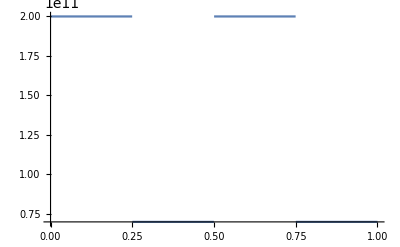

```mathematica
Plot[Y[x],{x,0,1}]
```

```mathematica
rho[x_]:=Piecewise[{{7800, 0<=x<0.25},{7800,0.5≤ x<0.75}, {2700,0.25≤ x<0.5}, {2700,0.75≤ x<=1}}];
```

```mathematica
f[x_]:=Piecewise[{{10^5*Cos[4*Pi*(x-0.5)],0.375≤ x<0.625},{0,True}}];
```

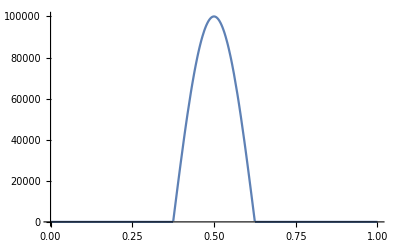

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
A = 10^-4*Pi;
g=9.81;
m=320.0;
```

```mathematica
innerIntegral[r_]:=  Integrate[rho[s]*A*g+f[s],{s,r,1},Assumptions->0<r<1];
```

```mathematica
Simplify[innerIntegral[r]]
```

Piecewise[{{15927.7-8.32114 r, 0.25≤r≤0.375}, {15931.7-24.0388 r, 0.<r<0.25}, {8.32114-8.32114 r, r≥0.75||r≤0}, {20.1094-24.0388 r, 0.625≤r<0.75}, {7977.86-24.0388 r-7957.75 Sin[12.5664 r], 0.5≤r<0.625}, {7970.-8.32114 r-7957.75 Sin[12.5664 r], True}}]

```mathematica
u[x_]:=Integrate[1/(Y[r]*A)*(m*g +innerIntegral[r]),{r,0,x},Assumptions->0<=x<=1]
```

```mathematica
uex =FullSimplify[u[x]]
```

Piecewise[{{-0.000140877+(0.000867028-1.89193×10^-7 x) x, 0.25<x≤0.375}, {(0.000303522-1.91295×10^-7 x) x, 0.<x≤0.25}, {0.000256813+(0.000050282-1.91295×10^-7 x) x, 0.625<x≤0.75}, {0.000187178+(0.000143127-1.89193×10^-7 x) x, 0.75<x≤1.}, {-5.17856×10^-6+(0.000505167-1.89193×10^-7 x) x+0.000028796 Cos[12.5664 x], 0.375<x≤0.5}, {0.000177656+(0.000176933-1.91295×10^-7 x) x+0.0000100786 Cos[12.5664 x], 0.5<x≤0.625}, {0., True}}]

```mathematica
uex
```

Piecewise[{{-0.000140877+(0.000867028-1.89193×10^-7 x) x, 0.25<x≤0.375}, {(0.000303522-1.91295×10^-7 x) x, 0.<x≤0.25}, {0.000256813+(0.000050282-1.91295×10^-7 x) x, 0.625<x≤0.75}, {0.000187178+(0.000143127-1.89193×10^-7 x) x, 0.75<x≤1.}, {-5.17856×10^-6+(0.000505167-1.89193×10^-7 x) x+0.000028796 Cos[12.5664 x], 0.375<x≤0.5}, {0.000177656+(0.000176933-1.91295×10^-7 x) x+0.0000100786 Cos[12.5664 x], 0.5<x≤0.625}, {0., True}}]

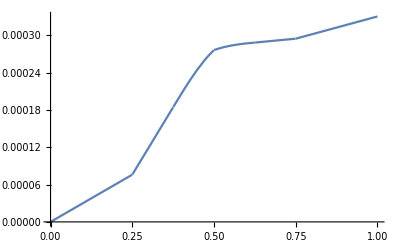

```mathematica
Plot[uex,{x,0,1}]
```

```mathematica
Sqrt[Integrate[uex^2,{x,0,1}]]
```

0.000233925

```mathematica
s^2/.{s-> 2}
```

4

```mathematica
Plot[u[x],{x,0,1}]
```